```mathematica
With[{g=ReadGrof[2]},
With[{full=FindEmptyFormula[g]},
Labeled[
Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindEmptyFormula[GContract[g,e]],e,full],{e,EdgeList[g]}]]]],
GraphHighlightStyle->"Thick",
ImageSize->600,
VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]],
Style[k,20,Bold]]
]
]
```

-Graphics-k

```mathematica
Table[StirlingS2[5,k],{k,6 }]
```

{1,15,25,10,1,0}

```mathematica
BellB[6]
```

203

```mathematica
With[{g=ReadGrof[3]},
{
With[{full=FindEmptyFormula[g]},
With[{allBad=DeleteDuplicates[Flatten[Table[AugmentedFormula[FindEmptyFormula[GContract[g,e]],e,full],{e,EdgeList[GraphComplement[g]]}]]]},
Labeled[Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[FormulaGraphReverse2[allBad]],
GraphHighlightStyle->"Thick",
ImageSize->600,
VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]],
Length[Select[allBad,SymbolLevel[#]==5&]]
]
]
],
With[{full=FindFullFormula[g]},
Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindFullFormula[GContract[g,e]],e,full],{e,EdgeList[g]}]]]],
GraphHighlightStyle->"Thick",
ImageSize->600,
VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
]}
]
```

{-Graphics-12,-Graphics-}

```mathematica
With[{g=ReadGrof[5]},
{
With[{full=FindEmptyFormula[g]},
With[{allBad=DeleteDuplicates[Flatten[Table[AugmentedFormula[FindEmptyFormula[GContract[g,e]],e,full],{e,EdgeList[g]}]]]},
{Select[allBad,SymbolLevel[#]==5&],Length[Select[allBad,SymbolLevel[#]==5&]],StirlingS2[VertexCount[g],5]}
]
],
With[{full=FindFullFormula[g]},
Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindFullFormula[GContract[g,e]],e,full],{e,EdgeList[g]}]]]],
GraphHighlightStyle->"Thick",
ImageSize->600,
VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
]}
]
```

{{{v1x267x3x4x5,v127x3x4x5x6,v17x26x3x4x5,v126x3x4x5x7,v1x257x3x4x6,v157x2x3x4x6,v17x25x3x4x6,v125x3x4x6x7,v12x3x4x57x6,v1x256x3x4x7,v12x3x4x56x7,v1x237x4x5x6,v137x2x4x5x6,v17x23x4x5x6,v123x4x5x6x7,v13x27x4x5x6,v12x37x4x5x6,v1x236x4x5x7,v136x2x4x5x7,v13x26x4x5x7,v12x36x4x5x7,v1x235x4x6x7,v135x2x4x6x7,v13x25x4x6x7,v12x35x4x6x7,v1x26x3x4x57,v1x23x4x57x6,v13x2x4x57x6,v1x2x3x4x567,v1x27x3x4x56,v17x2x3x4x56,v1x23x4x56x7,v13x2x4x56x7,v1x2x3x456x7,v12x3x46x5x7,v12x3x45x6x7,v1x246x3x5x7,v1x27x3x46x5,v17x2x3x46x5,v1x25x3x46x7,v1x23x46x5x7,v13x2x46x5x7,v1x2x3x46x57,v1x2x3x457x6,v1x245x3x6x7,v1x27x3x45x6,v17x2x3x45x6,v1x26x3x45x7,v1x23x45x6x7,v13x2x45x6x7,v1x2x357x4x6,v1x26x37x4x5,v1x25x37x4x6,v1x2x37x4x56,v1x2x37x46x5,v1x2x37x45x6,v1x2x367x4x5,v1x2x356x4x7,v1x2x346x5x7,v12x34x5x6x7,v1x27x36x4x5,v17x2x36x4x5,v1x25x36x4x7,v1x2x36x4x57,v1x2x36x45x7,v1x2x345x6x7,v1x27x35x4x6,v17x2x35x4x6,v1x26x35x4x7,v1x2x35x46x7,v1x2x347x5x6,v1x234x5x6x7,v134x2x5x6x7,v1x27x34x5x6,v17x2x34x5x6,v1x26x34x5x7,v1x25x34x6x7,v1x2x34x57x6,v1x2x34x56x7},79,140},-Graphics-}

```mathematica
Table[StirlingS2[7,k],{k,6 }]
```

{1,63,301,350,140,21}

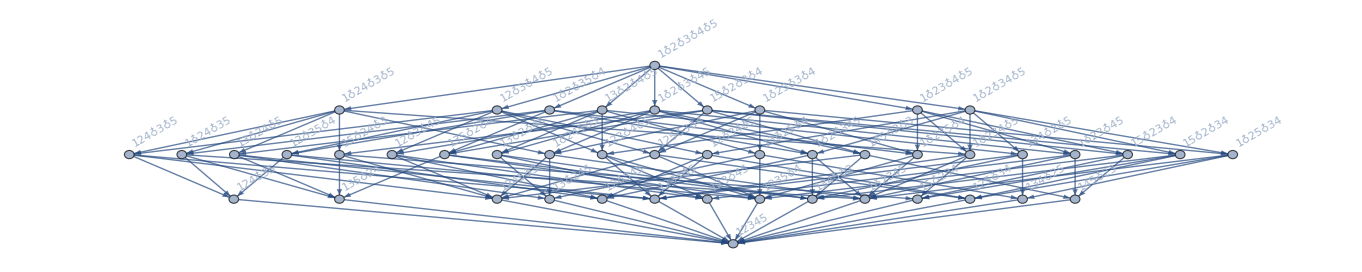

```mathematica
FindEmptyFormula[ReadGrof[2]]//FormulaGraphReverse2
```